### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={50,100,200}; (*мощности слоев*)
slopes = {0Degree, 0.5 Degree, 0 Degree, 0 Degree, -0.5 Degree, -0.7 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = -1 ;
```

```mathematica
(*folding parametres *)
hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =3; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
listV = {1500,2200,2500,2700, 2900, 3000,3100}; 
velocityTrend = {4,3,2,1.5,1.2,1,1};(*1 or 0*)
velocityAnomaly ={0,0,0,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "max"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
```

```mathematica
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Placed[Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], {Above}],
						PlotLabel -> "Глубинный разрез",FrameLabel->{"x, м","z, м"}, AspectRatio->1.1};
PlotDepthSection[horizons, optsDepth]
```

```mathematica
Show[ListLinePlot[Table[{time[[i, j, 1]], -time[[i, j, 2]]}, {i, Length[time]}, {j, Length[time[[i]]]}], optsDepth],
			ListLinePlot[Table[{time[[i, j, 1]], -time[[i, j, 2]]}, {i, Length[time]}, {j, Length[time[[i]]]}], {PlotStyle -> {Directive[Thickness[0.004], Black]}, PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],ImageSize -> 500}], {Frame -> True,
			FrameStyle -> Directive[14, Black], FrameLabel->{"x, м","z, м"},
			PlotRangePadding -> {{Scaled[0.05], Scaled[0.2]}, {Scaled[0.05], Scaled[0.05]}}}
]
```

-Graphics-

### VELOCITY

```mathematica
(*timeR = Table[{time[[i, j, 1]], -time[[i, j, 2]]*1000}, {i, Length[time]}, {j, Length[time[[i]]]}];*)
```

```mathematica
velModel=VelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
```

```mathematica
PlotVelocity[velModel, horizons]
```

```mathematica
datasetVelModel=VelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

$Aborted

### TIME

```mathematica
time=TimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Placed[Map["t " <> ToString[#] &, (Range[Length[time]] - 1)], Above],
						PlotLabel -> "Временной разрез", AspectRatio->1.1, FrameLabel-> {"x, м", "t, с"}};PlotTimeSection[time, optsTime]
```

### WELLS

```mathematica
wellDataset = WellSet[horizons, time, wellCount, wellType][["ds"]]
positions = WellSet[horizons, time,  wellCount, wellType][["positions"]]
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Placed[Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], {Above}],
						GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},GridLinesStyle->Directive[RGBColor["#405591"],Dashed,Thick],											
											PlotLabel -> "Распределение скважин"}, AspectRatio->1.1, FrameLabel-> {"x, м", "h, м"}]
```

{100,4100,5100,6600,8000,9200,10100}

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

```mathematica
x
```

### HTMethod

```mathematica
Clear[t];
lmSetHT=HTMethod2D[wellDataset,time, t][["lmSet"]]
dO=HTMethod2D[wellDataset,time, t][["depthObjective"]]
dPr=HTMethod2D[wellDataset,time, t][["depthPredicted"]]
lmParametresHT=HTMethod2D[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod2D[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod2D[wellDataset, time, t][["wellValues"]];
RSquared=HTMethod2D[wellDataset, time, t][["RSquared"]]
```

{FittedModel[2.28643+2746.03 t],FittedModel[17.0702+2695.95 t],FittedModel[84.2581+2616.48 t],FittedModel[434.164+2234.5 t]}

{{-292.765,-554.765,-366.765,-868.765,-854.765,-672.765,-95.7648},{-974.765,-1216.76,-1324.76,-1531.76,-1717.76,-1550.76,-984.765},{-1372.76,-1479.76,-1606.76,-1796.76,-1906.76,-1702.76,-1305.76},{-2001.76,-2106.76,-2110.76,-2230.76,-2239.76,-2088.76,-1937.76}}

{{-297.625,-563.519,-359.575,-881.054,-844.377,-663.869,-96.3347},{-971.794,-1225.18,-1316.09,-1537.72,-1710.96,-1555.09,-984.531},{-1363.76,-1490.,-1597.29,-1798.5,-1899.78,-1714.25,-1307.78},{-1990.9,-2101.78,-2101.94,-2227.53,-2237.98,-2113.21,-1943.01}}

{0.999044,0.999487,0.998434,0.988199}

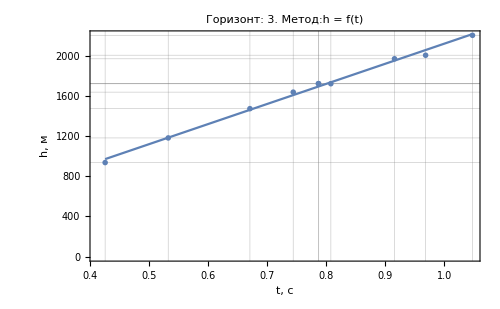
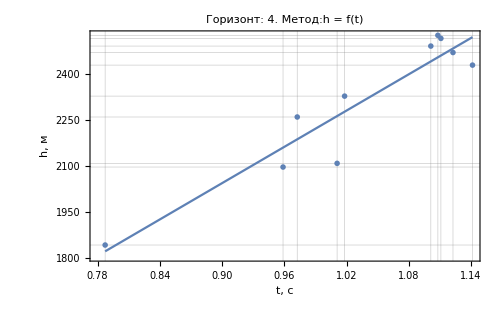
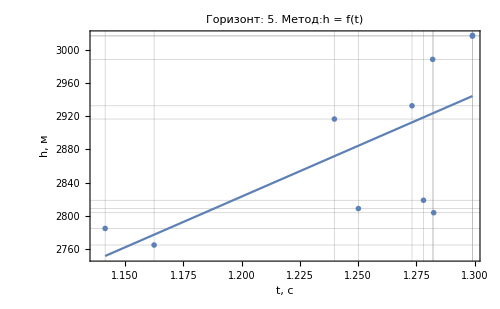
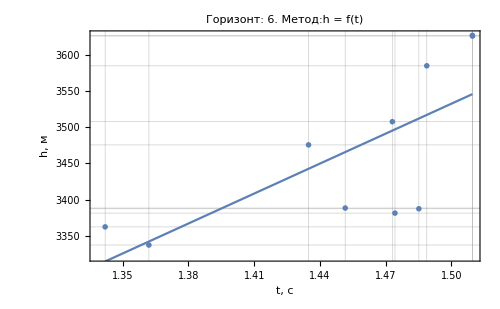
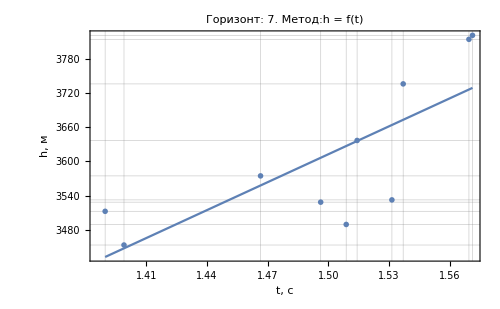
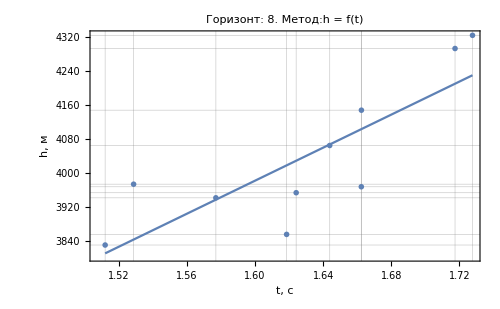

```mathematica
LinearRegressionPlots[wellValuesHT[[All,All, 2;;3]],lmSetHT, t, "h = f(t)", {"t, с","h, м"}]
```

### VTMethod

```mathematica
lmSetVT=VTMethod2D[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod2D[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod2D[wellDataset,time, t][["wellValues"]]
resultVT = VTMethod2D[wellDataset, time, t][["result"]];
fitsVT = VTMethod2D[wellDataset, time, t][["fits"]];
```

{FittedModel[2785.7-114.453 t],FittedModel[2774.34-85.46 t],FittedModel[2918.69-265.753 t],FittedModel[3409.94-792.58 t]}

{{{1,0.107551,2722.1},{1,0.20438,2714.38},{1,0.130111,2818.86},{1,0.320014,2714.77},{1,0.306657,2787.36},{1,0.240923,2792.45},{1,0.0342488,2796.15}},{{2,0.354132,2752.54},{2,0.44812,2715.27},{2,0.481839,2749.39},{2,0.564048,2715.66},{2,0.628307,2733.96},{2,0.570492,2718.3},{2,0.358857,2744.17}},{{3,0.489016,2807.2},{3,0.537263,2754.26},{3,0.57827,2778.57},{3,0.65517,2742.44},{3,0.693879,2747.98},{3,0.622972,2733.29},{3,0.467623,2792.35}},{{4,0.696684,2873.27},{4,0.746303,2822.93},{4,0.746375,2828.02},{4,0.802582,2779.48},{4,0.80726,2774.53},{4,0.751422,2779.75},{4,0.675252,2869.69}}}

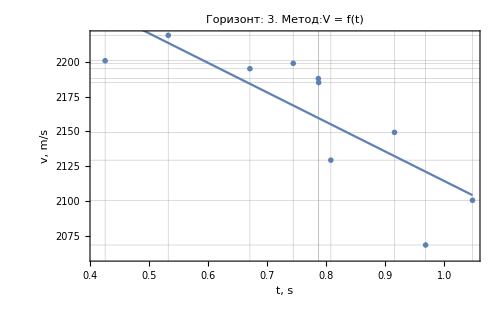
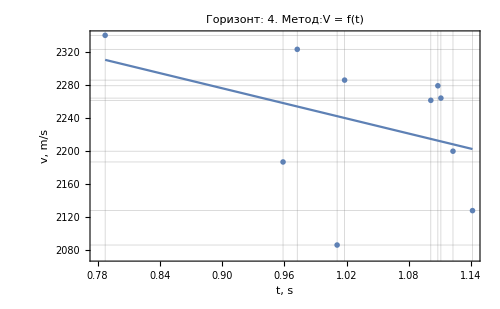
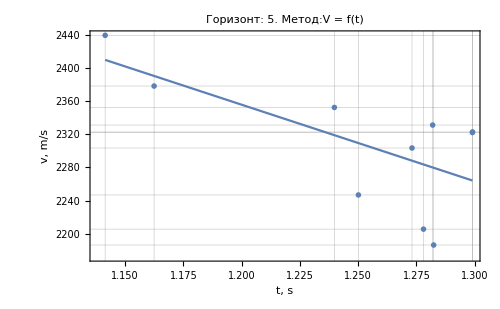
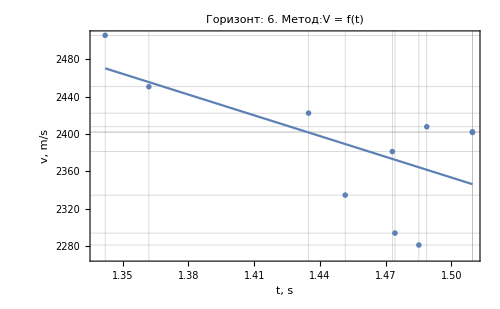
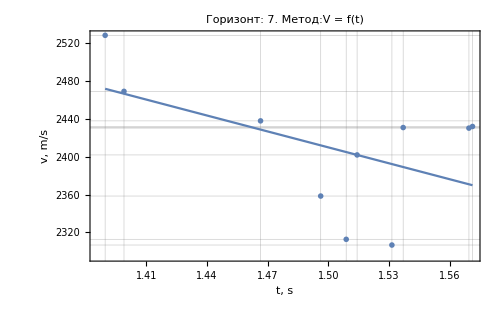
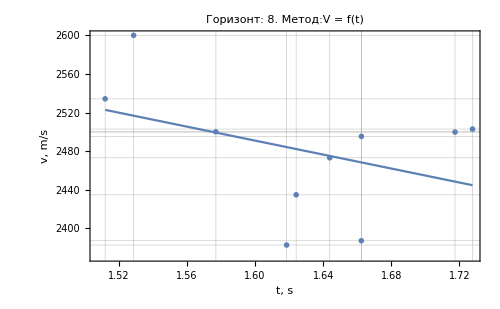

```mathematica
LinearRegressionPlots[wellValuesVT[[All, All,2;;3]],lmSetVT, t, "V = f(t)", {"t, s","v, m/s"}]
```

### THMethod

```mathematica
Clear[h];
lmSetTH=THMethod2D[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod2D[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod2D[wellDataset, time, h][["wellValues"]];
resultTH=THMethod2D[wellDataset, time, h][["result"]];
```

{FittedModel[-0.000648224+0.000363814 h],FittedModel[-0.00607894+0.000370736 h],FittedModel[-0.0312479+0.000381595 h],FittedModel[-0.183198+0.000442247 h]}

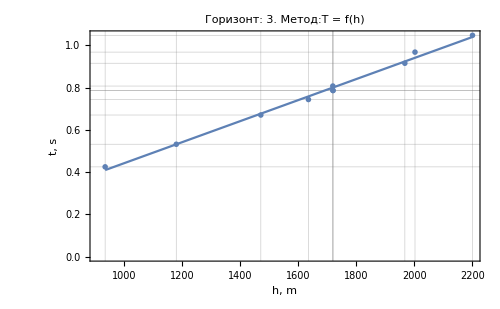
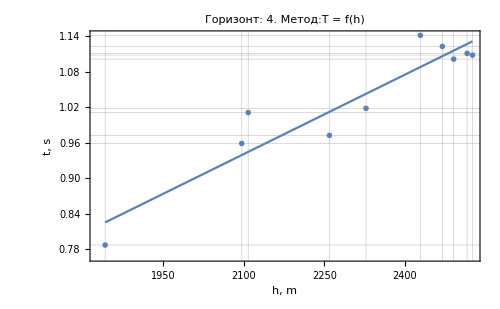
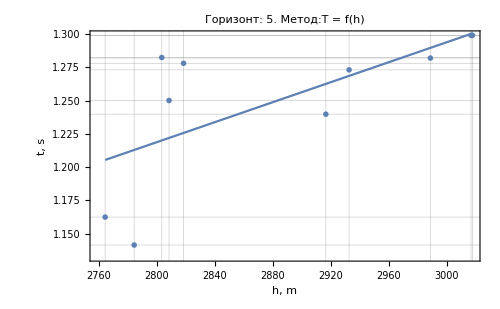
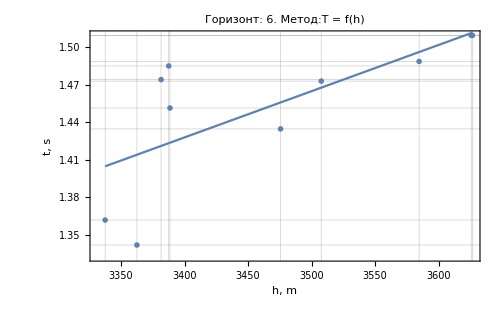
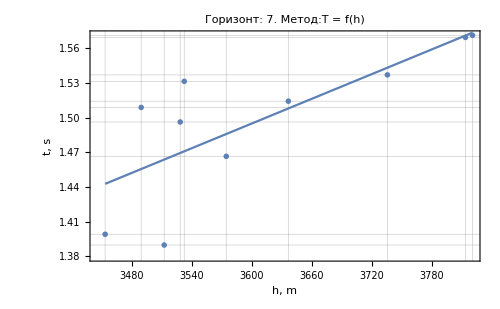
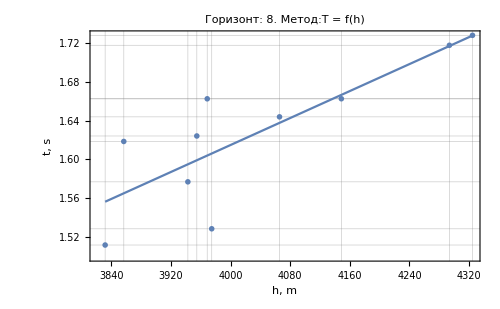

```mathematica
LinearRegressionPlots[wellValuesTH[[All, All,2;;3]],lmSetTH, h, "T = f(h)", {"h, m","t, s"}]
```

```mathematica
(*TimesBy[wellValuesTH[[All,All,2]],1000]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod2D[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod2D[wellDataset, time][["result"]];
fitsVave = VaveMethod2D[wellDataset, time][["fits"]];
```

{2763.73,2732.76,2765.16,2818.24}

### VaveVOGTMethod

```mathematica
Clear[v];
lmSetVaveVOGT=VaveRegressionMethod2D[wellDataset, time, vOGT, v][["lmSet"]]
lmParametresVaveVOGT=VaveRegressionMethod2D[wellDataset, time, vOGT, v][["lmParametres"]];
wellValuesVaveVOGT= VaveRegressionMethod2D[wellDataset, time, vOGT, v][["wellValues"]];
resultVaveVOGT=VaveRegressionMethod2D[wellDataset,  time, vOGT, v][["result"]];
plotDataVaveVOGT=VaveRegressionMethod2D[wellDataset,  time, vOGT, v][["plotData"]];
```

Part::pspec1: Part specification lmSet is not applicable.

VaveRegressionMethod2D[,{{{0,0},{100,0},{200,0},{300,0},{400,0},{500,0},{600,0},{700,0},{800,0},{900,0},{1000,0},{1100,0},{1200,0},{1300,0},{1400,0},{1500,0},{1600,0},{1700,0},{1800,0},{1900,0},{2000,0},{2100,0},{2200,0},{2300,0},{2400,0},{2500,0},{2600,0},{2700,0},{2800,0},{2900,0},{3000,0},{3100,0},{3200,0},{3300,0},{3400,0},{3500,0},{3600,0},{3700,0},{3800,0},{3900,0},{4000,0},{4100,0},{4200,0},{4300,0},{4400,0},{4500,0},{4600,0},{4700,0},{4800,0},{4900,0},{5000,0},{5100,0},{5200,0},{5300,0},{5400,0},{5500,0},{5600,0},{5700,0},{5800,0},{5900,0},{6000,0},{6100,0},{6200,0},{6300,0},{6400,0},{6500,0},{6600,0},{6700,0},{6800,0},{6900,0},{7000,0},{7100,0},{7200,0},{7300,0},{7400,0},{7500,0},{7600,0},{7700,0},{7800,0},{7900,0},{8000,0},{8100,0},{8200,0},{8300,0},{8400,0},{8500,0},{8600,0},{8700,0},{8800,0},{8900,0},{9000,0},{9100,0},{9200,0},{9300,0},{9400,0},{9500,0},{9600,0},{9700,0},{9800,0},{9900,0},{10000,0}},{{0,0.215102},{100,0.31212},{200,0.420639},{300,0.535074},{400,0.617549},{500,0.685359},{600,0.774609},{700,0.797902},{800,0.809945},{900,0.798451},{1000,0.789839},{1100,0.809042},{1200,0.805609},{1300,0.826563},{1400,0.897633},{1500,1.00293},{1600,1.10155},{1700,1.12092},{1800,1.11451},{1900,1.10857},{2000,1.0764},{2100,1.06671},{2200,1.06212},{2300,1.07444},{2400,1.05875},{2500,0.974036},{2600,0.875215},{2700,0.747006},{2800,0.653774},{2900,0.615304},{3000,0.560898},{3100,0.588207},{3200,0.624485},{3300,0.639811},{3400,0.664978},{3500,0.619569},{3600,0.563198},{3700,0.483817},{3800,0.425581},{3900,0.40932},{4000,0.408759},{4100,0.445842},{4200,0.499241},{4300,0.576489},{4400,0.659073},{4500,0.635457},{4600,0.593331},{4700,0.491523},{4800,0.374055},{4900,0.298322},{5000,0.260222},{5100,0.393626},{5200,0.605173},{5300,0.857874},{5400,1.05498},{5500,1.14817},{5600,1.15164},{5700,1.02751},{5800,0.918213},{5900,0.862264},{6000,0.82659},{6100,0.802648},{6200,0.739353},{6300,0.682515},{6400,0.652926},{6500,0.640028},{6600,0.649346},{6700,0.666203},{6800,0.706864},{6900,0.710781},{7000,0.729992},{7100,0.822706},{7200,0.904218},{7300,0.927751},{7400,0.935939},{7500,0.876872},{7600,0.804618},{7700,0.716216},{7800,0.630859},{7900,0.613315},{8000,0.70033},{8100,0.831453},{8200,0.970228},{8300,1.17744},{8400,1.33257},{8500,1.42563},{8600,1.3111},{8700,1.10669},{8800,0.840307},{8900,0.630376},{9000,0.509271},{9100,0.481846},{9200,0.525459},{9300,0.607551},{9400,0.707393},{9500,0.787506},{9600,0.785446},{9700,0.710529},{9800,0.521547},{9900,0.298451},{10000,0.0684976}},{{0,0.708265},{100,0.759154},{200,0.817005},{300,0.880526},{400,0.940925},{500,0.99742},{600,1.05501},{700,1.09669},{800,1.1329},{900,1.16168},{1000,1.18886},{1100,1.21854},{1200,1.24432},{1300,1.274},{1400,1.31164},{1500,1.3552},{1600,1.39866},{1700,1.42127},{1800,1.43315},{1900,1.43847},{2000,1.43084},{2100,1.42014},{2200,1.40266},{2300,1.38143},{2400,1.3487},{2500,1.29623},{2600,1.24061},{2700,1.18203},{2800,1.13323},{2900,1.09447},{3000,1.05772},{3100,1.03326},{3200,1.01434},{3300,0.996628},{3400,0.982929},{3500,0.959598},{3600,0.938644},{3700,0.918169},{3800,0.905049},{3900,0.898714},{4000,0.896239},{4100,0.897308},{4200,0.901301},{4300,0.909765},{4400,0.92284},{4500,0.918609},{4600,0.914124},{4700,0.907062},{4800,0.910962},{4900,0.930297},{5000,0.963679},{5100,1.01037},{5200,1.07446},{5300,1.15946},{5400,1.24744},{5500,1.30713},{5600,1.33055},{5700,1.31083},{5800,1.2909},{5900,1.27234},{6000,1.24887},{6100,1.22181},{6200,1.18773},{6300,1.15823},{6400,1.13887},{6500,1.1281},{6600,1.12777},{6700,1.13482},{6800,1.15066},{6900,1.1646},{7000,1.18041},{7100,1.20632},{7200,1.23013},{7300,1.24096},{7400,1.24659},{7500,1.23757},{7600,1.23019},{7700,1.22706},{7800,1.23465},{7900,1.25661},{8000,1.29009},{8100,1.33271},{8200,1.37822},{8300,1.44006},{8400,1.49345},{8500,1.52565},{8600,1.46805},{8700,1.38485},{8800,1.30093},{8900,1.23702},{9000,1.18583},{9100,1.14098},{9200,1.10214},{9300,1.07303},{9400,1.05137},{9500,1.03255},{9600,0.995656},{9700,0.937787},{9800,0.857004},{9900,0.781096},{10000,0.717714}},{{0,0.978032},{100,1.00957},{200,1.04672},{300,1.08815},{400,1.12918},{500,1.16899},{600,1.21464},{700,1.24779},{800,1.27888},{900,1.30599},{1000,1.33216},{1100,1.36153},{1200,1.38559},{1300,1.41073},{1400,1.44098},{1500,1.47496},{1600,1.50737},{1700,1.51884},{1800,1.52093},{1900,1.51991},{2000,1.5094},{2100,1.50071},{2200,1.4901},{2300,1.47985},{2400,1.46152},{2500,1.42544},{2600,1.38611},{2700,1.34304},{2800,1.30692},{2900,1.27737},{3000,1.24707},{3100,1.22561},{3200,1.20768},{3300,1.18965},{3400,1.17498},{3500,1.15072},{3600,1.12753},{3700,1.10554},{3800,1.08958},{3900,1.07976},{4000,1.07453},{4100,1.07492},{4200,1.07961},{4300,1.09222},{4400,1.11151},{4500,1.11491},{4600,1.11811},{4700,1.11674},{4800,1.12161},{4900,1.1358},{5000,1.15654},{5100,1.18231},{5200,1.21924},{5300,1.27491},{5400,1.33483},{5500,1.37258},{5600,1.38296},{5700,1.35982},{5800,1.34612},{5900,1.34206},{6000,1.33926},{6100,1.33699},{6200,1.32765},{6300,1.31871},{6400,1.31367},{6500,1.31034},{6600,1.31058},{6700,1.31274},{6800,1.3189},{6900,1.32183},{7000,1.32805},{7100,1.34646},{7200,1.36692},{7300,1.37856},{7400,1.38847},{7500,1.38515},{7600,1.38214},{7700,1.37923},{7800,1.38014},{7900,1.38776},{8000,1.40196},{8100,1.42038},{8200,1.4423},{8300,1.48328},{8400,1.52273},{8500,1.55075},{8600,1.49801},{8700,1.42661},{8800,1.36},{8900,1.31471},{9000,1.27927},{9100,1.24594},{9200,1.21511},{9300,1.18846},{9400,1.16926},{9500,1.15357},{9600,1.12459},{9700,1.08076},{9800,1.02079},{9900,0.97041},{10000,0.935245}},{{0,1.39337},{100,1.41353},{200,1.43733},{300,1.46407},{400,1.48773},{500,1.50878},{600,1.535},{700,1.54798},{800,1.55885},{900,1.56501},{1000,1.57219},{1100,1.58247},{1200,1.58942},{1300,1.5987},{1400,1.61576},{1500,1.63918},{1600,1.66298},{1700,1.66989},{1800,1.67007},{1900,1.6698},{2000,1.66478},{2100,1.66355},{2200,1.66236},{2300,1.6656},{2400,1.66201},{2500,1.64265},{2600,1.62204},{2700,1.5983},{2800,1.58144},{2900,1.57107},{3000,1.55925},{3100,1.55625},{3200,1.5554},{3300,1.55171},{3400,1.55074},{3500,1.53816},{3600,1.52462},{3700,1.51033},{3800,1.50077},{3900,1.49535},{4000,1.49261},{4100,1.49282},{4200,1.49605},{4300,1.50457},{4400,1.51783},{4500,1.51323},{4600,1.50648},{4700,1.49387},{4800,1.48619},{4900,1.4872},{5000,1.49275},{5100,1.50472},{5200,1.52784},{5300,1.57106},{5400,1.62055},{5500,1.64921},{5600,1.65253},{5700,1.62431},{5800,1.60891},{5900,1.6052},{6000,1.6048},{6100,1.6063},{6200,1.60279},{6300,1.60037},{6400,1.60191},{6500,1.60516},{6600,1.6114},{6700,1.61819},{6800,1.62762},{6900,1.6326},{7000,1.63799},{7100,1.6544},{7200,1.66974},{7300,1.67381},{7400,1.67478},{7500,1.66052},{7600,1.64528},{7700,1.63021},{7800,1.61901},{7900,1.61452},{8000,1.6181},{8100,1.62723},{8200,1.64199},{8300,1.67716},{8400,1.71419},{8500,1.74253},{8600,1.69343},{8700,1.62904},{8800,1.5721},{8900,1.53979},{9000,1.51929},{9100,1.50284},{9200,1.49018},{9300,1.48365},{9400,1.48453},{9500,1.48888},{9600,1.47924},{9700,1.45339},{9800,1.40939},{9900,1.37366},{10000,1.3505}}},vOGT,v]⟦lmSet⟧

Part::pspec1: Part specification lmParametres is not applicable.

Part::pspec1: Part specification wellValues is not applicable.

Part::pspec1: Part specification result is not applicable.

Part::pspec1: Part specification plotData is not applicable.

### GRAPHICS

```mathematica
opts1 = {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000, FrameLabel->{"x, м", "z, м"},FrameStyle->Directive[16, Black], LabelStyle->Directive[16, Black], 
					PlotLabels -> Placed[Map["" <> ToString[#] &, (Range[Length[horizons]] - 1)], {After}],PlotStyle->Gray, AspectRatio->1.1};
opts2= {PlotStyle->{Blue},PlotLegends->{"H = f(t)"}};
opts3 = {PlotStyle->{Orange}, PlotLegends->{"V = f(t)"}};
opts4 = {PlotStyle->{Green}, PlotLegends->{"T = f(h)"}};
opts5 = { PlotStyle->{Red}, PlotLegends->{"Vave"}};
allHorizons = {horizons,resultHT, resultVave};
opts = {opts1, opts2, opts5};
PlotPredictionModel2D[wellDataset, allHorizons, opts]
```

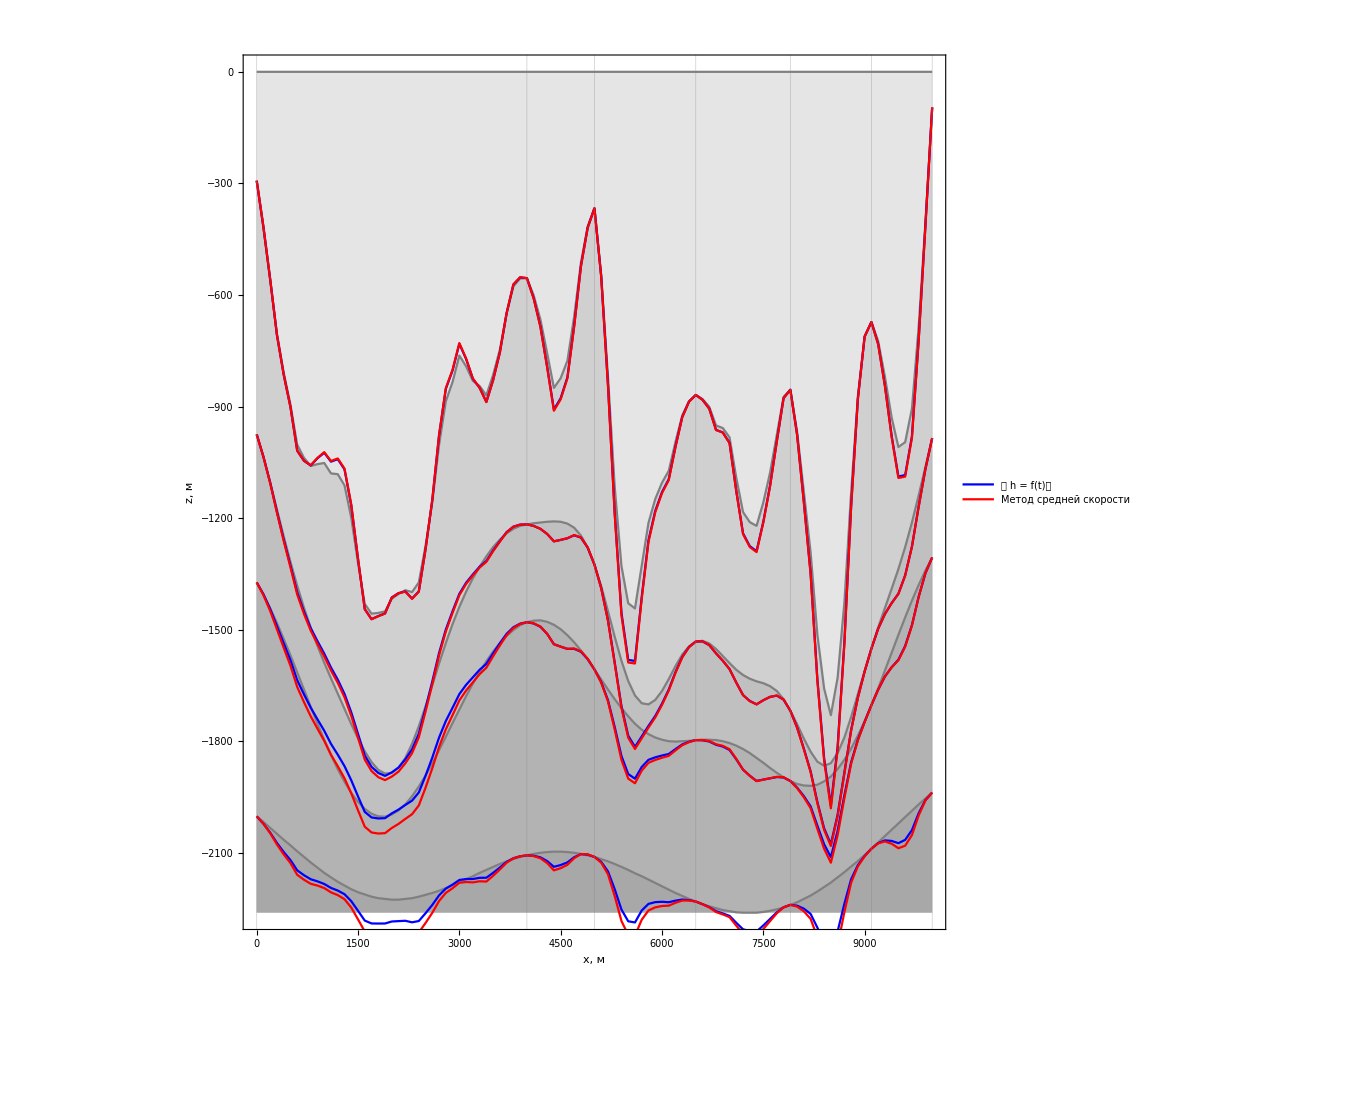

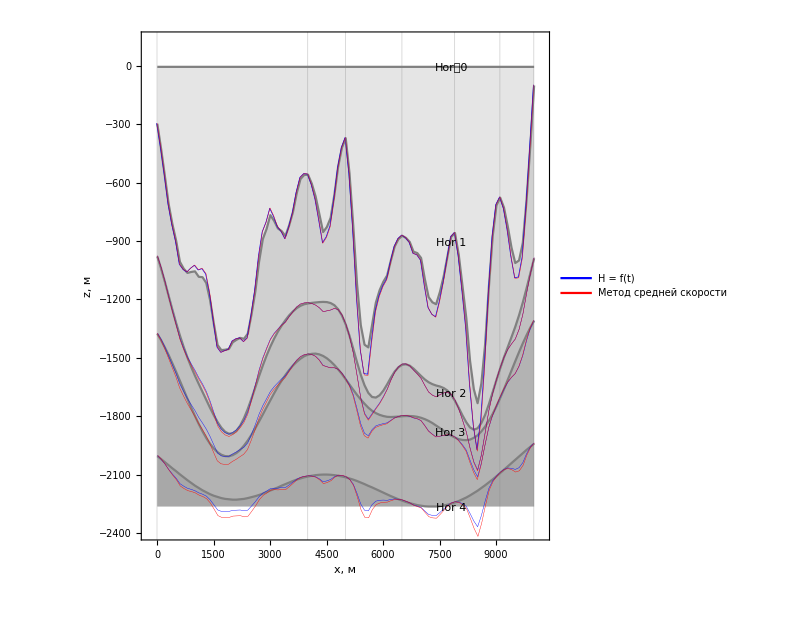

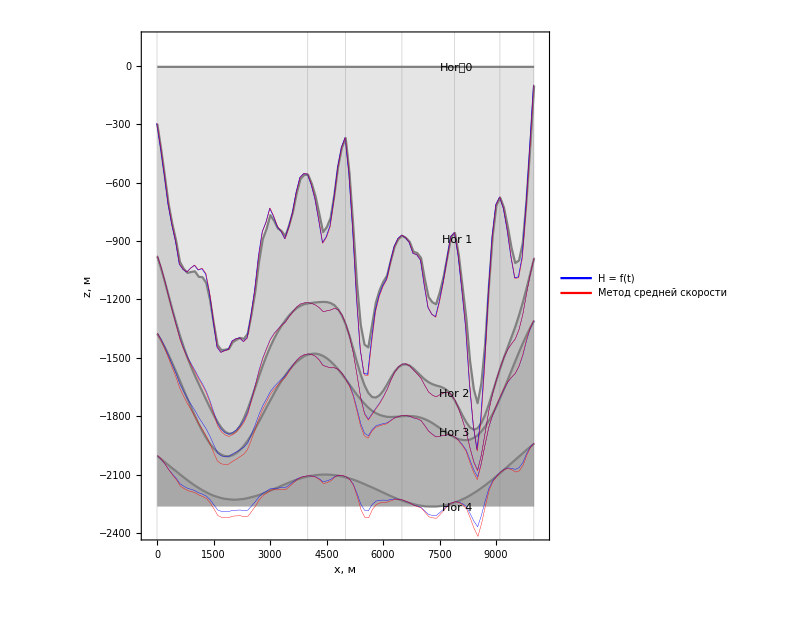

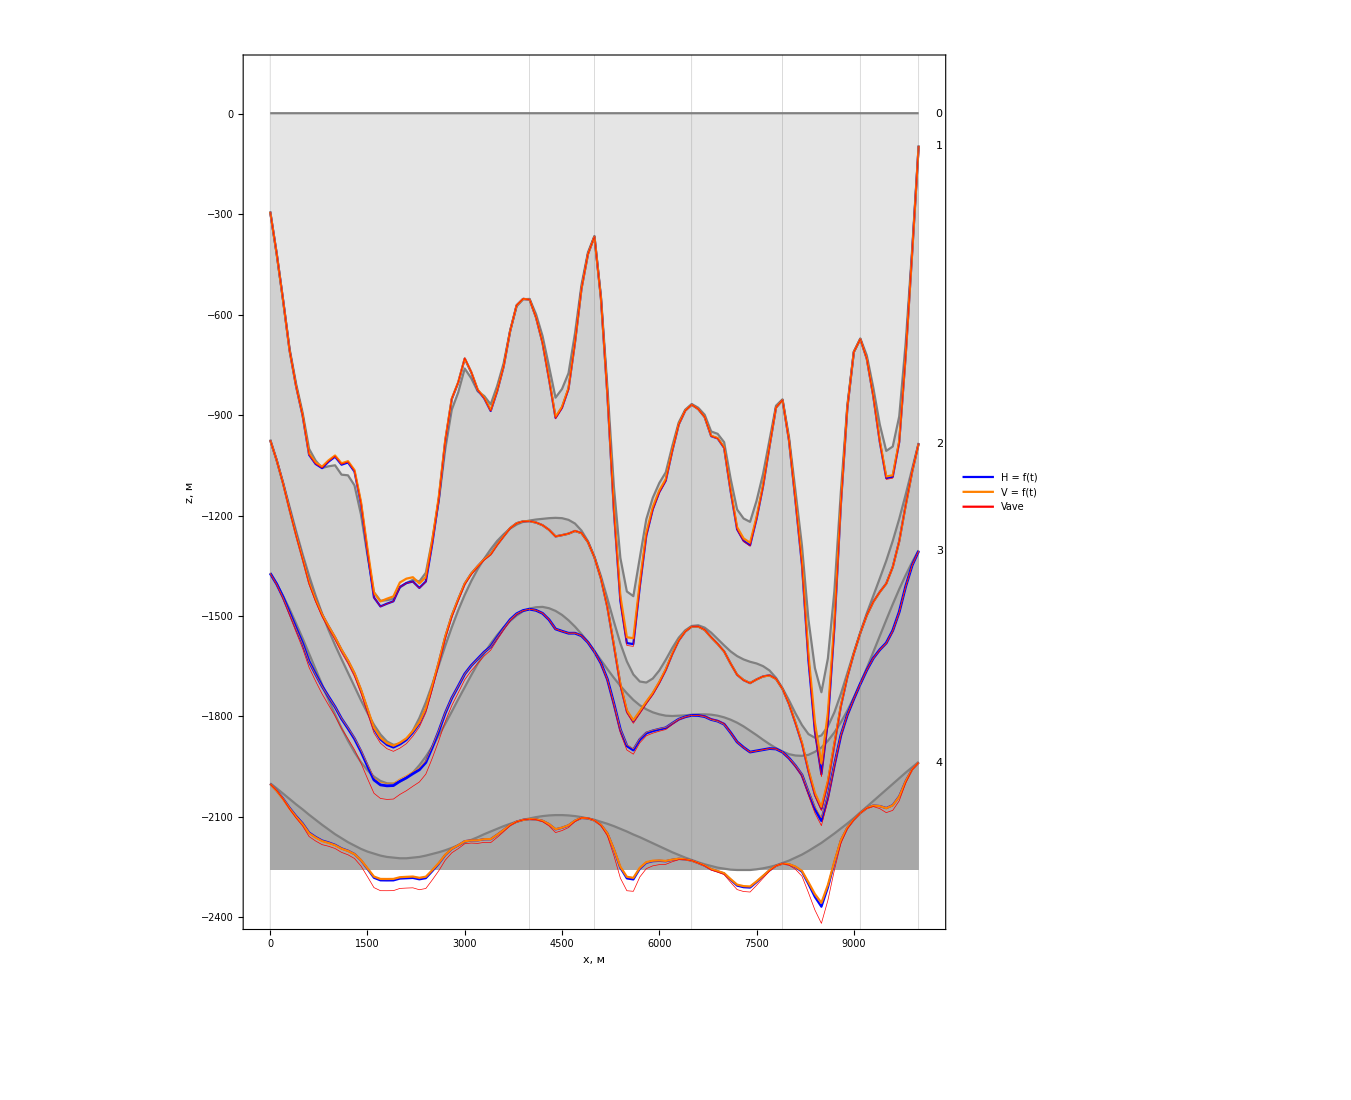

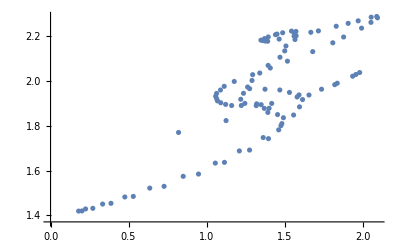

```mathematica
ListPlot[Table[{time[[2,i,2]],time[[3,i,2]]}, {i,Length[time[[2]]]}]]
```

```mathematica
Table[{time[[2,i,2]],time[[3,i,2]]}, {i,Length[time[[2]]]}]
```

{{1.27602,1.96619},{1.37457,1.96384},{1.46954,1.96048},{1.53114,1.94957},{1.59244,1.93843},{1.61511,1.9176},{1.59559,1.88507},{1.55772,1.84862},{1.47659,1.80091},{1.36299,1.7479},{1.20999,1.68814},{1.05596,1.63366},{0.850243,1.57452},{0.635962,1.52193},{0.476216,1.48227},{0.333932,1.4506},{0.224499,1.42875},{0.179933,1.41922},{0.201343,1.41989},{0.271108,1.43159},{0.387368,1.45392},{0.530439,1.48476},{0.727695,1.52989},{0.948358,1.58474},{1.1146,1.63703},{1.27557,1.69196},{1.39675,1.743},{1.46216,1.78225},{1.48269,1.81022},{1.49259,1.83646},{1.45495,1.85054},{1.39263,1.86021},{1.36983,1.87825},{1.31851,1.89051},{1.24532,1.90054},{1.21903,1.91889},{1.23661,1.94565},{1.26294,1.97377},{1.29116,2.00288},{1.34085,2.03629},{1.39461,2.07035},{1.47054,2.1068},{1.50098,2.13516},{1.50873,2.15706},{1.56666,2.18599},{1.57394,2.20257},{1.56366,2.21232},{1.5728,2.22201},{1.54423,2.22363},{1.48768,2.21618},{1.45139,2.21039},{1.44181,2.2076},{1.39531,2.19747},{1.37141,2.19022},{1.34854,2.18316},{1.36152,2.18126},{1.37552,2.17935},{1.39143,2.17835},{1.46515,2.18793},{1.5607,2.20181},{1.66813,2.21827},{1.71672,2.22458},{1.8309,2.24533},{1.90757,2.25824},{1.97179,2.2695},{2.05506,2.28585},{2.09052,2.28906},{2.09524,2.28297},{2.05359,2.26263},{1.99336,2.23682},{1.87833,2.19729},{1.80902,2.17137},{1.68028,2.13189},{1.51812,2.08927},{1.40841,2.05869},{1.29543,2.02887},{1.17732,1.99858},{1.11304,1.97687},{1.08908,1.96022},{1.06409,1.945},{1.05812,1.93247},{1.06451,1.92169},{1.06992,1.91175},{1.09069,1.90337},{1.12219,1.89606},{1.16061,1.89103},{1.22269,1.89118},{1.32119,1.89854},{1.35005,1.8948},{1.41738,1.9003},{1.5804,1.92929},{1.73679,1.96385},{1.83749,1.99064},{1.95688,2.02974},{1.98115,2.03855},{1.9363,2.02186},{1.8214,1.9842},{1.65636,1.93798},{1.40073,1.87873},{1.12494,1.82365},{0.820414,1.77056}}

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVaveVOGT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave = f(vOGT)"]
```

Part::pspec1: Part specification result is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::pkspec1: The expression Charting`ChartLabelingDump`getLength[result] cannot be used as a part specification.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: «1» is not a list of numbers or pairs of numbers.

ListLinePlot[VaveRegressionMethod2D[,{{{0,0},{100,0},{200,0},{300,0},{400,0},{500,0},{600,0},{700,0},{800,0},{900,0},{1000,0},{1100,0},{1200,0},{1300,0},{1400,0},{1500,0},{1600,0},{1700,0},{1800,0},{1900,0},{2000,0},{2100,0},{2200,0},{2300,0},{2400,0},{2500,0},{2600,0},{2700,0},{2800,0},{2900,0},{3000,0},{3100,0},{3200,0},{3300,0},{3400,0},{3500,0},{3600,0},{3700,0},{3800,0},{3900,0},{4000,0},{4100,0},{4200,0},{4300,0},{4400,0},{4500,0},{4600,0},{4700,0},{4800,0},{4900,0},{5000,0},{5100,0},{5200,0},{5300,0},{5400,0},{5500,0},{5600,0},{5700,0},{5800,0},{5900,0},{6000,0},{6100,0},{6200,0},{6300,0},{6400,0},{6500,0},{6600,0},{6700,0},{6800,0},{6900,0},{7000,0},{7100,0},{7200,0},{7300,0},{7400,0},{7500,0},{7600,0},{7700,0},{7800,0},{7900,0},{8000,0},{8100,0},{8200,0},{8300,0},{8400,0},{8500,0},{8600,0},{8700,0},{8800,0},{8900,0},{9000,0},{9100,0},{9200,0},{9300,0},{9400,0},{9500,0},{9600,0},{9700,0},{9800,0},{9900,0},{10000,0}},{{0,1.6359},{100,1.68693},{200,1.96711},{300,2.27389},{400,2.12222},{500,1.44724},{600,0.819516},{700,0.54716},{800,0.533257},{900,0.487547},{1000,0.527058},{1100,0.788453},{1200,0.994337},{1300,1.24866},{1400,1.53036},{1500,1.53886},{1600,1.34388},{1700,1.33245},{1800,1.39837},{1900,1.41815},{2000,1.54892},{2100,1.46508},{2200,1.12699},{2300,0.869271},{2400,0.652193},{2500,0.414422},{2600,0.194325},{2700,0.0881451},{2800,0.106356},{2900,0.254048},{3000,0.426467},{3100,0.398649},{3200,0.237482},{3300,0.318352},{3400,0.74373},{3500,1.16773},{3600,1.18971},{3700,0.840508},{3800,0.546986},{3900,0.506593},{4000,0.425672},{4100,0.303553},{4200,0.371965},{4300,0.727779},{4400,1.11168},{4500,1.12371},{4600,1.08732},{4700,1.16269},{4800,1.24946},{4900,1.39921},{5000,1.30599},{5100,1.1256},{5200,1.09582},{5300,1.15624},{5400,1.31576},{5500,1.20205},{5600,0.810407},{5700,0.637939},{5800,0.734947},{5900,0.94132},{6000,0.672626},{6100,0.110018},{6200,0.0734203},{6300,0.363229},{6400,0.545972},{6500,0.618359},{6600,0.591865},{6700,0.495273},{6800,0.568577},{6900,0.752079},{7000,0.824012},{7100,0.820469},{7200,0.775702},{7300,0.758084},{7400,0.566885},{7500,0.419633},{7600,0.523857},{7700,0.764963},{7800,1.20714},{7900,1.60585},{8000,1.60104},{8100,1.25716},{8200,0.976317},{8300,0.885741},{8400,0.853124},{8500,0.875211},{8600,0.887147},{8700,0.787225},{8800,0.693469},{8900,0.745263},{9000,0.808817},{9100,0.678707},{9200,0.422488},{9300,0.383943},{9400,0.510856},{9500,0.59792},{9600,0.740462},{9700,0.886104},{9800,0.959626},{9900,0.934859},{10000,0.822123}},{{0,2.28864},{100,2.26834},{200,2.28072},{300,2.32194},{400,2.20132},{500,1.94713},{600,1.76146},{700,1.64958},{800,1.58672},{900,1.54745},{1000,1.54573},{1100,1.59674},{1200,1.6647},{1300,1.75782},{1400,1.86703},{1500,1.91779},{1600,1.91942},{1700,1.93544},{1800,1.93871},{1900,1.90982},{2000,1.87921},{2100,1.78923},{2200,1.63863},{2300,1.49767},{2400,1.36443},{2500,1.23705},{2600,1.13079},{2700,1.06151},{2800,1.02969},{2900,1.03375},{3000,1.06388},{3100,1.08706},{3200,1.10613},{3300,1.15594},{3400,1.24943},{3500,1.36035},{3600,1.38822},{3700,1.33587},{3800,1.30236},{3900,1.30524},{4000,1.31039},{4100,1.32665},{4200,1.37405},{4300,1.4617},{4400,1.57197},{4500,1.62831},{4600,1.68078},{4700,1.74609},{4800,1.79891},{4900,1.84877},{5000,1.844},{5100,1.8161},{5200,1.7937},{5300,1.76443},{5400,1.74411},{5500,1.67009},{5600,1.55017},{5700,1.46277},{5800,1.41051},{5900,1.38326},{6000,1.28925},{6100,1.18133},{6200,1.15033},{6300,1.16733},{6400,1.19309},{6500,1.21834},{6600,1.23589},{6700,1.2453},{6800,1.27525},{6900,1.32293},{7000,1.36027},{7100,1.38583},{7200,1.4045},{7300,1.42829},{7400,1.43464},{7500,1.45726},{7600,1.51191},{7700,1.58567},{7800,1.69059},{7900,1.8033},{8000,1.81868},{8100,1.75147},{8200,1.69919},{8300,1.66612},{8400,1.63066},{8500,1.59361},{8600,1.55329},{8700,1.49485},{8800,1.44017},{8900,1.41307},{9000,1.39846},{9100,1.36406},{9200,1.32339},{9300,1.32021},{9400,1.34532},{9500,1.37309},{9600,1.41479},{9700,1.4609},{9800,1.49517},{9900,1.5105},{10000,1.50927}},{{0,2.44943},{100,2.4343},{200,2.46961},{300,2.54911},{400,2.48213},{500,2.28922},{600,2.16324},{700,2.10265},{800,2.07503},{900,2.04725},{1000,2.03332},{1100,2.05069},{1200,2.06662},{1300,2.09379},{1400,2.13241},{1500,2.11556},{1600,2.0626},{1700,2.04168},{1800,2.03033},{1900,2.00913},{2000,2.00695},{2100,1.96306},{2200,1.87075},{2300,1.79718},{2400,1.73193},{2500,1.66786},{2600,1.61018},{2700,1.57034},{2800,1.54885},{2900,1.54722},{3000,1.55727},{3100,1.54755},{3200,1.52843},{3300,1.54244},{3400,1.60705},{3500,1.69835},{3600,1.71737},{3700,1.66766},{3800,1.64687},{3900,1.66489},{4000,1.67983},{4100,1.6944},{4200,1.72932},{4300,1.79826},{4400,1.88197},{4500,1.90463},{4600,1.91787},{4700,1.94531},{4800,1.97024},{4900,2.00226},{5000,1.98735},{5100,1.95706},{5200,1.94548},{5300,1.94173},{5400,1.95302},{5500,1.91595},{5600,1.83519},{5700,1.78911},{5800,1.77811},{5900,1.78894},{6000,1.72523},{6100,1.63839},{6200,1.61854},{6300,1.63757},{6400,1.65395},{6500,1.6615},{6600,1.65915},{6700,1.65186},{6800,1.66978},{6900,1.70782},{7000,1.73325},{7100,1.74849},{7200,1.75914},{7300,1.77495},{7400,1.76943},{7500,1.77313},{7600,1.80335},{7700,1.84789},{7800,1.92662},{7900,2.01847},{8000,2.02224},{8100,1.95427},{8200,1.91129},{8300,1.89526},{8400,1.88539},{8500,1.87924},{8600,1.87216},{8700,1.84764},{8800,1.82374},{8900,1.8212},{9000,1.82184},{9100,1.79496},{9200,1.75651},{9300,1.74783},{9400,1.76054},{9500,1.77135},{9600,1.79147},{9700,1.81608},{9800,1.83114},{9900,1.83198},{10000,1.82014}},{{0,2.56906},{100,2.56431},{200,2.60859},{300,2.69703},{400,2.63758},{500,2.45077},{600,2.33021},{700,2.27293},{800,2.24653},{900,2.21926},{1000,2.20377},{1100,2.21822},{1200,2.22983},{1300,2.2534},{1400,2.28771},{1500,2.26727},{1600,2.21141},{1700,2.18965},{1800,2.17816},{1900,2.15749},{2000,2.15791},{2100,2.11797},{2200,2.03099},{2300,1.96411},{2400,1.90692},{2500,1.85023},{2600,1.8013},{2700,1.76887},{2800,1.75411},{2900,1.75858},{3000,1.7727},{3100,1.76435},{3200,1.74529},{3300,1.75735},{3400,1.818},{3500,1.90263},{3600,1.91294},{3700,1.85388},{3800,1.82168},{3900,1.82689},{4000,1.82971},{4100,1.83145},{4200,1.85351},{4300,1.91023},{4400,1.98308},{4500,1.99621},{4600,2.00058},{4700,2.02189},{4800,2.04274},{4900,2.07203},{5000,2.05784},{5100,2.02963},{5200,2.02081},{5300,2.02258},{5400,2.04143},{5500,2.0126},{5600,1.94075},{5700,1.90494},{5800,1.9035},{5900,1.92388},{6000,1.86973},{6100,1.79105},{6200,1.778},{6300,1.80177},{6400,1.82085},{6500,1.82905},{6600,1.82532},{6700,1.8139},{6800,1.82634},{6900,1.85687},{7000,1.87411},{7100,1.87978},{7200,1.88088},{7300,1.88643},{7400,1.87065},{7500,1.86545},{7600,1.88747},{7700,1.92516},{7800,1.99772},{7900,2.08546},{8000,2.08718},{8100,2.01855},{8200,1.97698},{8300,1.96372},{8400,1.95662},{8500,1.95532},{8600,1.95238},{8700,1.9327},{8800,1.91361},{8900,1.9152},{9000,1.91997},{9100,1.89651},{9200,1.85943},{9300,1.8521},{9400,1.86479},{9500,1.8742},{9600,1.89223},{9700,1.91337},{9800,1.92498},{9900,1.92098},{10000,1.9043}},{{0,2.65492},{100,2.65229},{200,2.69957},{300,2.79173},{400,2.73732},{500,2.55622},{600,2.44136},{700,2.39042},{800,2.37166},{900,2.35202},{1000,2.34481},{1100,2.3675},{1200,2.38865},{1300,2.42109},{1400,2.46556},{1500,2.45461},{1600,2.40888},{1700,2.39723},{1800,2.39519},{1900,2.38462},{2000,2.39512},{2100,2.36525},{2200,2.28705},{2300,2.22894},{2400,2.17924},{2500,2.12938},{2600,2.08602},{2700,2.05786},{2800,2.04676},{2900,2.05231},{3000,2.06627},{3100,2.05712},{3200,2.03472},{3300,2.04154},{3400,2.09569},{3500,2.17255},{3600,2.17385},{3700,2.10387},{3800,2.06012},{3900,2.05382},{4000,2.04385},{4100,2.03282},{4200,2.04276},{4300,2.08801},{4400,2.14939},{4500,2.15233},{4600,2.14842},{4700,2.16209},{4800,2.17657},{4900,2.20204},{5000,2.18402},{5100,2.15517},{5200,2.14696},{5300,2.14998},{5400,2.17199},{5500,2.14695},{5600,2.08015},{5700,2.05004},{5800,2.0543},{5900,2.081},{6000,2.0319},{6100,1.95892},{6200,1.95029},{6300,1.97786},{6400,2.00009},{6500,2.01019},{6600,2.00708},{6700,1.99566},{6800,2.00746},{6900,2.03545},{7000,2.04888},{7100,2.05075},{7200,2.04677},{7300,2.04789},{7400,2.02704},{7500,2.01614},{7600,2.03244},{7700,2.06507},{7800,2.13319},{7900,2.21712},{8000,2.21505},{8100,2.14388},{8200,2.09913},{8300,2.0846},{8400,2.07686},{8500,2.07555},{8600,2.07261},{8700,2.05418},{8800,2.03699},{8900,2.03984},{9000,2.04649},{9100,2.02493},{9200,1.98973},{9300,1.98429},{9400,1.99887},{9500,2.00954},{9600,2.02946},{9700,2.05186},{9800,2.06346},{9900,2.06009},{10000,2.04403}}},vOGT,v]⟦result⟧,GridLines→{{200,1300,1600,1800,3500,3700,3800,5200,7900,8200},None},Filling→Bottom,Frame→True,ImageSize→500,PlotLabels→{Hor 0,Hor 1,Hor 2,Hor 3,Hor 4,Hor 5},PlotLabel→Vave = f(vOGT)]